### Numerical analysis

#### Setting the parameter

```mathematica
Subscript[a, u]=Subscript[a, d]=0.546;Subscript[m, u]=Subscript[m, d]=0.007;b=0.474;Subscript[m, 0]=√0.8;Subscript[α, s]=0.434;W=√2.25;
μ=0.5;Λ=0.1;
x[M2_]:=W^2/M2
Subscript[e, 0][M2_]:=1-E^(-x[M2])
Subscript[e, 1][M2_]:=1-(1+x[M2])E^(-x[M2])
Subscript[e, 2][M2_]:=1-(1+x[M2]+1/2(x[M2])^2)E^(-x[M2])
L[M2_]:=Log[M2/Λ^2]/Log[μ^2/Λ^2]
```

#### Contribution of the continuum

```mathematica
delta1[M2_]:=(M2^3/8(L[M2])^(-4/9)(1-Subscript[e, 2][M2])+b M2/32(L[M2])^(-4/9)(1-Subscript[e, 0][M2])-(Subscript[m, d] Subscript[a, d] M2)/4(L[M2])^(-4/9)(1-Subscript[e, 0][M2]))/(M2^3/8(L[M2])^(-4/9)+(b M2)/32(L[M2])^(-4/9)+Subscript[a, u]^2/6(L[M2])^(4/9)-(Subscript[a, u]^2 Subscript[m, 0]^2)/(24M2)(L[M2])^(-2/27)-(Subscript[m, d] Subscript[a, d] M2)/4(L[M2])^(-4/9)-(Subscript[m, d] Subscript[a, d] Subscript[m, 0]^2)/24(L[M2])^(-26/27)-(Subscript[m, u] Subscript[a, u] Subscript[m, 0]^2)/12(L[M2])^(-26/27))
delta2[M2_]:=((Subscript[a, d] M2^2)/4(1-Subscript[e, 1][M2])+(Subscript[m, d] M2^3)/4(L[M2])^(-8/9)(1-Subscript[e, 2][M2])-(Subscript[m, d] b M2)/32(1-Subscript[e, 0][M2])(L[M2])^(-8/9))/((Subscript[a, d] M2^2)/4-(Subscript[a, d] b)/72+34/81 Subscript[α, s]/π(Subscript[a, u]^2 Subscript[a, d])/M2(L[M2])^(-1/9)+(Subscript[m, d] M2^3)/4(L[M2])^(-8/9)-(Subscript[m, d] b M2)/32(L[M2])^(-8/9)+(Subscript[m, d] Subscript[a, u]^2)/3+(Subscript[m, u] Subscript[a, u] Subscript[a, d])/2)
Plot[delta1[M2],{M2,√0.6,√2}];
M2list=Range[0.6,1.2,0.1];
delta1[M2list]
delta2[M2list]
```

{0.097908,0.165343,0.241849,0.320736,0.397065,0.467849,0.53167}

{0.0886599,0.146483,0.208317,0.269647,0.327959,0.382071,0.431583}

#### Masses of proton and neutron

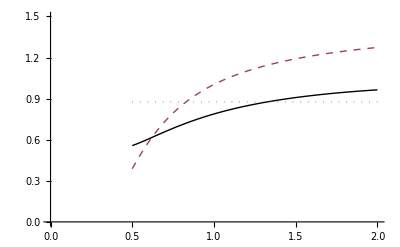

```mathematica
ci=0.0036;Subscript[m, em]=√0.048;Subscript[a, q]=0.546;
fm1[M2_]:=Log[((1+4/9 ci)M2^3)/8(L[M2])^(-4/9)Subscript[e, 2][M2]+(b M2)/32(L[M2])^(-4/9)Subscript[e, 0][M2]+Subscript[a, u]^2/6(L[M2])^(4/9)-(Subscript[a, u]^2 Subscript[m, 0]^2)/(24M2)(L[M2])^(-2/27)-(Subscript[m, d] Subscript[a, d] M2)/4(L[M2])^(-4/9)Subscript[e, 0][M2]-(Subscript[m, d] Subscript[a, d] Subscript[m, 0]^2)/24(L[M2])^(-26/27)-(Subscript[m, u] Subscript[a, u] Subscript[m, 0]^2)/12(L[M2])^(-26/27)]
Mp2first[M2_]:=M2^2 Derivative[1][fm1][M2]
fm2[M2_]:=Log[((1+4/9 ci)Subscript[a, d] M2^2)/4 Subscript[e, 1][M2]-(Subscript[a, d] b)/72+(34 Subscript[α, s]/π Subscript[a, u]^2 Subscript[a, d])/(81M2)(L[M2])^(-1/9)+(Subscript[m, d] M2^3)/4(L[M2])^(-8/9)Subscript[e, 2][M2]-(Subscript[m, d] b M2)/32(L[M2])^(-8/9)Subscript[e, 0][M2]+(Subscript[m, d] Subscript[a, u]^2)/3+(Subscript[m, u] Subscript[a, u] Subscript[a, d])/2+(Subscript[m, em]^2 Subscript[a, q] M2 Subscript[e, 0][M2])/24]
Mp2second[M2_]:=M2^2 Derivative[1][fm2][M2]
Plot[{Mp2first[M2],Mp2second[M2],0.936^2},{M2,0.5,2.0},PlotStyle->{Black,Dashed,Dotted},AxesOrigin->{0,0},PlotRange->{{0,2},{0,1.5}}]
```